## sqrt action from n-action

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
L=m/(2 n)(-T'[s]^2+X'[s]^2)-(m n)/2;
```

```mathematica
soln=Solve[D[L,n]==0,n]
```

{{n→-√(T'[s]^2-X'[s]^2)},{n→√(T'[s]^2-X'[s]^2)}}

```mathematica
Simplify[L/.soln⟦1⟧]
```

m √(T'[s]^2-X'[s]^2)

## Solutions to eom in de Sitter

```mathematica
eta[t_]:=c4/(Cos[c1 t+c2]);
x[t_]:=c4 Tan[c2+c1 t]+c3;
```

```mathematica
(*check original eom*)
D[eta[t],{t,2}]-(D[eta[t],t]^2+D[x[t],t]^2)/eta[t]//Simplify
D[x[t],{t,2}]-2 D[eta[t],t]D[x[t],t]/eta[t]
```

0

0

```mathematica
solconst=Solve[{eta[0]==EA,eta[1]==EB,x[0]==XA,x[1]==XB},{c1,c2,c3,c4}]/.{C[1]->0,C[2]->0}//Simplify;
```

```mathematica
solINI=Simplify[solconst,XB>XA>0&&EA<EB<0]
```

{{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→-(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]},{c3→(-EA^2+EB^2+XA^2-XB^2)/(2 (XA-XB)),c4→(√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)))/(2 (XA-XB)),c1→ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))],c2→ArcTan[√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2)),EA^2-EB^2+(XA-XB)^2]}}

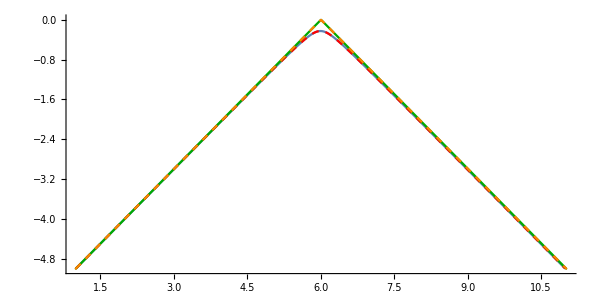

```mathematica
par1={EA->-5,EB->-5,XA->1,XB->10.99};
par2={EA->-5,EB->-5,XA->1,XB->11.01};
Show[ParametricPlot[{Re[x[t]/.solINI⟦1⟧/.par1],Re[eta[t]/.solINI⟦1⟧/.par1]},{t,0,1}],
ParametricPlot[{Re[x[t]/.solINI⟦2⟧/.par1],Re[eta[t]/.solINI⟦2⟧/.par1]},{t,0,1},PlotStyle->{Red, Dashed}],
ParametricPlot[{Re[x[t]/.solINI⟦1⟧/.par2],Re[eta[t]/.solINI⟦1⟧/.par2]},{t,0,1},PlotStyle->{Darker[Green]}],
ParametricPlot[{Re[x[t]/.solINI⟦2⟧/.par2],Re[eta[t]/.solINI⟦2⟧/.par2]},{t,0,1},PlotStyle->{Orange, Dashed}],ImageSize->600,PlotRange->All,AxesOrigin->{0,0}]
```

## Classical action in de Sitter

```mathematica
a[eta[s]]=-1/(H eta[s]);
L=FullSimplify[m/(2n)a[eta[s]]^2(-eta'[s]^2+x'[s]^2)-(m n)/2]
```

(c1^2 m)/(2 H^2 n)-(m n)/2

```mathematica
S=Integrate[L,{s,0,1}]
```

(c1^2 m)/(2 H^2 n)-(m n)/2

```mathematica
Scl[n_]=(c1^2 m)/(2 H^2 n)-(m n)/2;
```

```mathematica
solN=Solve[D[ Scl[n],n]==0,n]
```

{{n→-(ⅈ c1)/H},{n→(ⅈ c1)/H}}

```mathematica
ⅈ Scl[n]/.solN⟦1⟧(*/.solINI⟦1⟧*)
ⅈ Scl[n]/.solN⟦2⟧(*/.solINI⟦1⟧*)
```

-(c1 m)/H

(c1 m)/H

```mathematica
Simplify[{ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧,ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦2⟧},XB>XA>0&&EA<EB<0]
Simplify[{ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦1⟧,ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦2⟧},XB>XA>0&&EA<EB<0]
```

{-(m ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))])/H,-(m ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))])/H}

{(m ArcTan[EA^2+EB^2-(XA-XB)^2,√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))])/H,(m ArcTan[EA^2+EB^2-(XA-XB)^2,-√(-EA^4-(EB^2-(XA-XB)^2)^2+2 EA^2 (EB^2+(XA-XB)^2))])/H}

```mathematica
Simplify[ⅈ Scl[n]/.solN⟦1⟧]
```

-(c1 m)/H

```mathematica
Simplify[{ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧/.{EA->EB,XB->ΔX+XA},ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦2⟧/.{EA->EB,XB->ΔX+XA}},ΔX>0]
Simplify[{ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦1⟧/.{EA->EB,XB->ΔX+XA},ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦2⟧/.{EA->EB,XB->ΔX+XA}},ΔX>0]
```

{-(m ArcTan[2 EB^2-ΔX^2,ΔX √(4 EB^2-ΔX^2)])/H,-(m ArcTan[2 EB^2-ΔX^2,-ΔX √(4 EB^2-ΔX^2)])/H}

{(m ArcTan[2 EB^2-ΔX^2,ΔX √(4 EB^2-ΔX^2)])/H,(m ArcTan[2 EB^2-ΔX^2,-ΔX √(4 EB^2-ΔX^2)])/H}

## Saddle points and trajectories for separations smaller than critical:

```mathematica
par={EA->-5,EB->-5,XA->1,XB->10,H->0.1,m->1};
```

```mathematica
solN/.solINI⟦1⟧/.par//N
solN/.solINI⟦2⟧/.par//N
```

{{n→0.-22.3954 ⅈ},{n→0.+22.3954 ⅈ}}

{{n→0.+22.3954 ⅈ},{n→0.-22.3954 ⅈ}}

N is imaginary.

```mathematica
N[{Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧/.par]]^2,Abs[Exp[ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦1⟧/.par]]^2}]
N[{Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦2⟧/.par]]^2,Abs[Exp[ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦2⟧/.par]]^2}]
```

{3.52867×10^-20,2.83393×10^19}

{2.83393×10^19,3.52867×10^-20}

#### In order for the amplitude to be suppressed, the relevant SPs should be solN⟦1⟧ solINI⟦1⟧ and solN⟦2⟧ solINI⟦2⟧. To Check ✓

### Solution solINI⟦1⟧

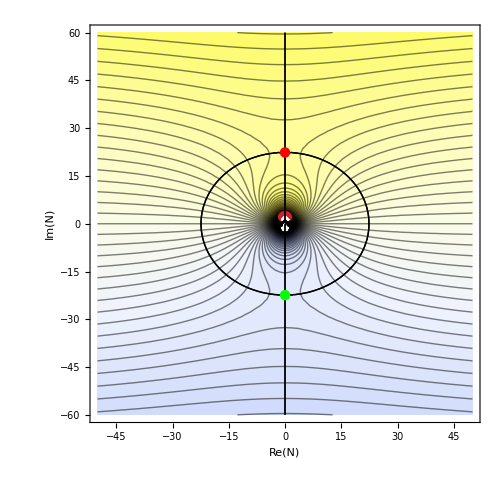

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->10,H->0.1,m->1};
α=0;
Im1=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦1⟧//.solINI⟦1⟧//.par];
Im2=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦2⟧//.solINI⟦1⟧//.par];
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦1⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/Exp[ⅈ α]/.solINI⟦1⟧//.par/.n->u+ⅈ v]=={Im1,Im2},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Red,Point[{Re[n//.solN⟦2⟧/.solINI⟦1⟧//.par],Im[n//.solN⟦2⟧/.solINI⟦1⟧//.par]}]}],Graphics[{PointSize[0.015],Green,Point[{Re[n//.solN⟦1⟧/.solINI⟦1⟧//.par],Im[n//.solN⟦1⟧/.solINI⟦1⟧//.par]}]}],Axes->True,ImageSize->500]
```

To break the degeneracy in the ascent and descent lines, we introduce a small perturbation

#### α=+10^-1

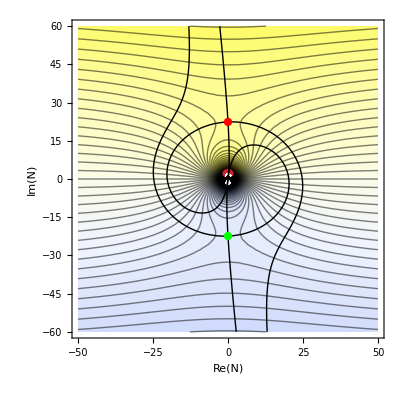

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->10,H->0.1,m->1};
α=10^-1;
Im1=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦1⟧//.solINI⟦1⟧//.par];
Im2=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦2⟧//.solINI⟦1⟧//.par];
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦1⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/Exp[ⅈ α]/.solINI⟦1⟧//.par/.n->u+ⅈ v]=={Im1,Im2},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Red,Point[{Re[n//.solN⟦2⟧/.solINI⟦1⟧//.par],Im[n//.solN⟦2⟧/.solINI⟦1⟧//.par]}]}],Graphics[{PointSize[0.015],Green,Point[{Re[n//.solN⟦1⟧/.solINI⟦1⟧//.par],Im[n//.solN⟦1⟧/.solINI⟦1⟧//.par]}]}],Axes->True,ImageSize->400]
```

#### α=-10^-1

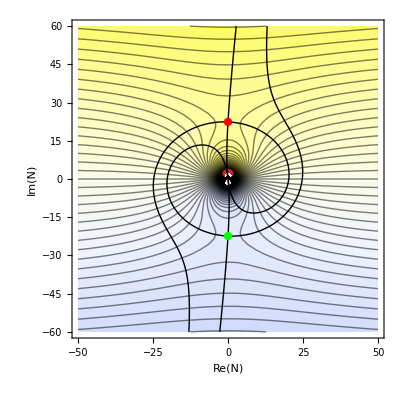

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->10,H->0.1,m->1};
α=-10^-1;
Im1=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦1⟧//.solINI⟦1⟧//.par];
Im2=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦2⟧//.solINI⟦1⟧//.par];
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦1⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/Exp[ⅈ α]/.solINI⟦1⟧//.par/.n->u+ⅈ v]=={Im1,Im2},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Red,Point[{Re[n//.solN⟦2⟧/.solINI⟦1⟧//.par],Im[n//.solN⟦2⟧/.solINI⟦1⟧//.par]}]}],Graphics[{PointSize[0.015],Green,Point[{Re[n//.solN⟦1⟧/.solINI⟦1⟧//.par],Im[n//.solN⟦1⟧/.solINI⟦1⟧//.par]}]}],Axes->True,ImageSize->400]
```

#### With either perturbation the lower SP is relevant, corresponding to solN⟦1⟧ solINI⟦1⟧

```mathematica
ParametricPlot3D[{Re[ x[s]/.solN⟦1⟧/.solINI⟦1⟧//.par],Re[ eta[s]/.solN⟦1⟧/.solINI⟦1⟧//.par],Im[ eta[s]/.solN⟦1⟧/.solINI⟦1⟧//.par]},{s,0,1},AxesLabel->{"Re(x)","Re(η)","Im(η)"},LabelStyle->texStyle,ImageSize->400,PlotStyle->{Blue}(*,AspectRatio->Automatic*)]
```

-Graphics3D-

Im[η]=0 for the whole trajectory!

### Solution solINI⟦2⟧

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->10,H->0.1,m->1};
α=0;
Im1=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦1⟧//.solINI⟦2⟧//.par];
Im2=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦2⟧//.solINI⟦2⟧//.par];
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦2⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/Exp[ⅈ α]/.solINI⟦2⟧//.par/.n->u+ⅈ v]=={Im1,Im2},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Green,Point[{Re[n//.solN⟦2⟧/.solINI⟦2⟧//.par],Im[n//.solN⟦2⟧/.solINI⟦2⟧//.par]}]}],Graphics[{PointSize[0.015],Red,Point[{Re[n//.solN⟦1⟧/.solINI⟦2⟧//.par],Im[n//.solN⟦1⟧/.solINI⟦2⟧//.par]}]}],Axes->True,ImageSize->500]
```

-Graphics-

To break the degeneracy in the ascent and descent lines, we introduce a small perturbation

#### α=+10^-1

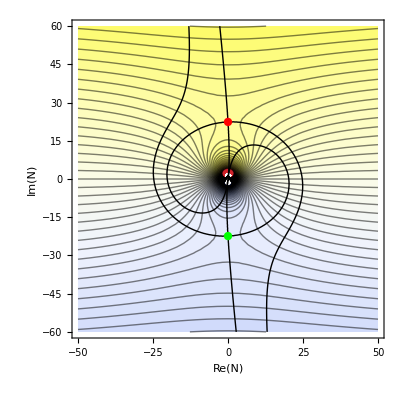

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->10,H->0.1,m->1};
α=10^-1;
Im1=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦1⟧//.solINI⟦2⟧//.par];
Im2=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦2⟧//.solINI⟦2⟧//.par];
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦2⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/Exp[ⅈ α]/.solINI⟦2⟧//.par/.n->u+ⅈ v]=={Im1,Im2},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Green,Point[{Re[n//.solN⟦2⟧/.solINI⟦2⟧//.par],Im[n//.solN⟦2⟧/.solINI⟦2⟧//.par]}]}],Graphics[{PointSize[0.015],Red,Point[{Re[n//.solN⟦1⟧/.solINI⟦2⟧//.par],Im[n//.solN⟦1⟧/.solINI⟦2⟧//.par]}]}],Axes->True,ImageSize->400]
```

#### α=-10^-1

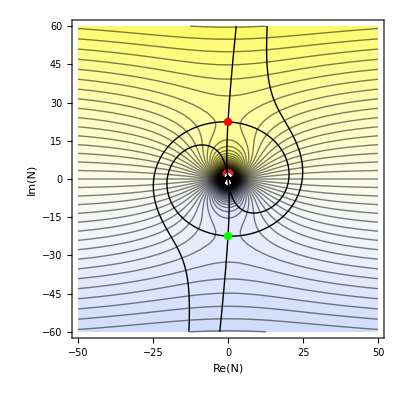

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->10,H->0.1,m->1};
α=-10^-1;
Im1=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦1⟧//.solINI⟦2⟧//.par];
Im2=Im[ⅈ Scl[n]/Exp[ⅈ α]//.solN⟦2⟧//.solINI⟦2⟧//.par];
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦2⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/Exp[ⅈ α]/.solINI⟦2⟧//.par/.n->u+ⅈ v]=={Im1,Im2},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Green,Point[{Re[n//.solN⟦2⟧/.solINI⟦2⟧//.par],Im[n//.solN⟦2⟧/.solINI⟦2⟧//.par]}]}],Graphics[{PointSize[0.015],Red,Point[{Re[n//.solN⟦1⟧/.solINI⟦2⟧//.par],Im[n//.solN⟦1⟧/.solINI⟦2⟧//.par]}]}],Axes->True,ImageSize->400]
```

#### With either perturbation the lower SP is relevant, corresponding to solN⟦2⟧ solINI⟦2⟧

```mathematica
ParametricPlot3D[{Re[ x[s]/.solN⟦2⟧/.solINI⟦2⟧//.par],Re[ eta[s]/.solN⟦2⟧/.solINI⟦2⟧//.par],Im[ eta[s]/.solN⟦2⟧/.solINI⟦2⟧//.par]},{s,0,1},AxesLabel->{"Re(x)","Re(η)","Im(η)"},LabelStyle->texStyle,ImageSize->400,PlotStyle->{Blue}(*,AspectRatio->Automatic*)]
```

-Graphics3D-

Im[η]=0 for the whole trajectory!

#### The two solutions for the constants c1...c4, i.e. solINI⟦1⟧ and solINI⟦2⟧, lead to the same trajectory.

## Saddle points and trajectories for separations larger than critical

```mathematica
par={EA->-5,EB->-5,XA->1,XB->12,H->0.1,m->1};
```

```mathematica
solN/.solINI⟦1⟧/.par//N
solN/.solINI⟦2⟧/.par//N
```

{{n→-8.87137-31.4159 ⅈ},{n→8.87137+31.4159 ⅈ}}

{{n→8.87137-31.4159 ⅈ},{n→-8.87137+31.4159 ⅈ}}

```mathematica
N[{Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧/.par]]^2,Abs[Exp[ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦1⟧/.par]]^2}]
N[{Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦2⟧/.par]]^2,Abs[Exp[ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦2⟧/.par]]^2}]
```

{5.1579×10^-28,1.93877×10^27}

{5.1579×10^-28,1.93877×10^27}

#### In order for the amplitude to be suppressed, the relevant SPs should be solN⟦1⟧ solINI⟦1⟧ and solN⟦1⟧ solINI⟦2⟧. Check ✓

### Solution solINI⟦1⟧

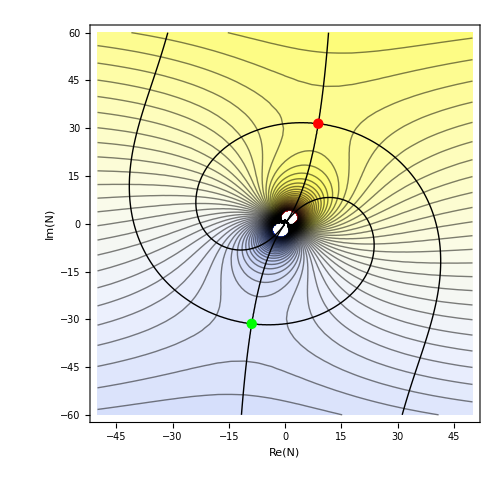

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->12,H->0.1,m->1};
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦1⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/.solINI⟦1⟧//.par/.n->u+ⅈ v]=={Im[ⅈ Scl[n]//.solN⟦1⟧//.solINI⟦1⟧//.par],
Im[ⅈ Scl[n]//.solN⟦2⟧//.solINI⟦1⟧//.par]},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Red,Point[{Re[n//.solN⟦2⟧/.solINI⟦1⟧//.par],Im[n//.solN⟦2⟧/.solINI⟦1⟧//.par]}]}],Graphics[{PointSize[0.015],Green,Point[{Re[n//.solN⟦1⟧/.solINI⟦1⟧//.par],Im[n//.solN⟦1⟧/.solINI⟦1⟧//.par]}]}],Axes->True,ImageSize->500]
```

```mathematica
ParametricPlot3D[{Re[ x[s]/.solN⟦1⟧/.solINI⟦1⟧//.par],Re[ eta[s]/.solN⟦1⟧/.solINI⟦1⟧//.par],Im[ eta[s]/.solN⟦1⟧/.solINI⟦1⟧//.par]},{s,0,1},AxesLabel->{"Re(x)","Re(η)","Im(η)"},LabelStyle->texStyle,ImageSize->400,PlotStyle->{Blue}(*,AspectRatio->Automatic*)]
```

-Graphics3D-

### Solution solINI⟦2⟧

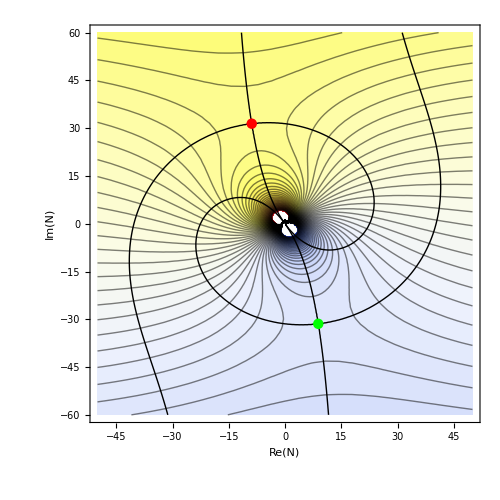

```mathematica
texStyle={FontSize->14,FontColor->Black};
par={EA->-5,EB->-5,XA->1,XB->12,H->0.1,m->1};
Show[ContourPlot[Re[ⅈ Scl[n]/.solINI⟦2⟧//.par/.n->u+ⅈ v],{u,-50,50},{v,-60,60},Contours->80,ColorFunction->"TemperatureMap",Frame-> True, AxesLabel->{"Re(N)","Im(N)"},Axes->True,LabelStyle->texStyle],
ContourPlot[Im[ⅈ Scl[n]/.solINI⟦2⟧//.par/.n->u+ⅈ v]=={Im[ⅈ Scl[n]/.solN⟦2⟧/.solINI⟦2⟧//.par],
Im[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦2⟧//.par]},{u,-50,50},{v,-60,60},PlotPoints->50,Axes->True,AxesStyle->Black,ContourStyle->{{Black,Thick},{Black,Thick}}],Graphics[{PointSize[0.015],Red,Point[{Re[n/.solN⟦2⟧/.solINI⟦2⟧//.par],Im[n/.solN⟦2⟧/.solINI⟦2⟧//.par]}]}],Graphics[{PointSize[0.015],Green,Point[{Re[n/.solN⟦1⟧/.solINI⟦2⟧//.par],Im[n/.solN⟦1⟧/.solINI⟦2⟧//.par]}]}],Axes->True,ImageSize->500]
```

```mathematica
ParametricPlot3D[{Re[ x[s]/.solN⟦1⟧/.solINI⟦2⟧//.par],Re[ eta[s]/.solN⟦1⟧/.solINI⟦2⟧//.par],Im[ eta[s]/.solN⟦1⟧/.solINI⟦2⟧//.par]},{s,0,1},AxesLabel->{"Re(x)","Re(η)","Im(η)"},LabelStyle->texStyle,ImageSize->400,PlotStyle->{Blue}(*,AspectRatio->Automatic*)]
```

-Graphics3D-

#### The difference between the two solutions for the constants c1...c4, i.e. between solINI⟦1⟧ and solINI⟦2⟧, is that the trajectory goes to either positive or negative imaginary η. They are symmetric about Im[η]=0.

## Amplitude

#### Vary probability wrt. separation for different H={0.1,1,10}

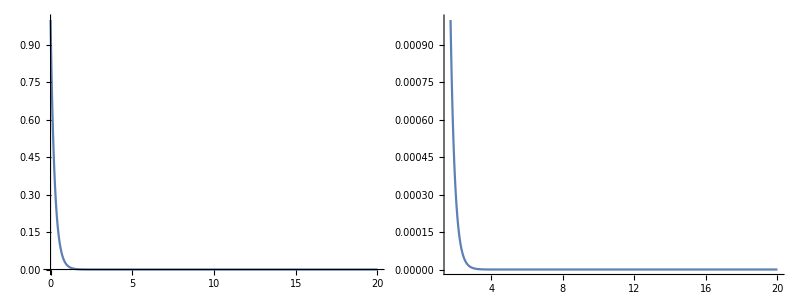

```mathematica
parl={EA->-5,EB->-5,XA->1,XB->XA+l,H->0.1,m->1};
Grid[{{Plot[Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧//.parl]]^2,{l,0,20},PlotRange->All,ImageSize->400],Plot[Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧//.parl]]^2,{l,0,20},PlotRange->{All,{0,0.001}},ImageSize->400]}}]
```

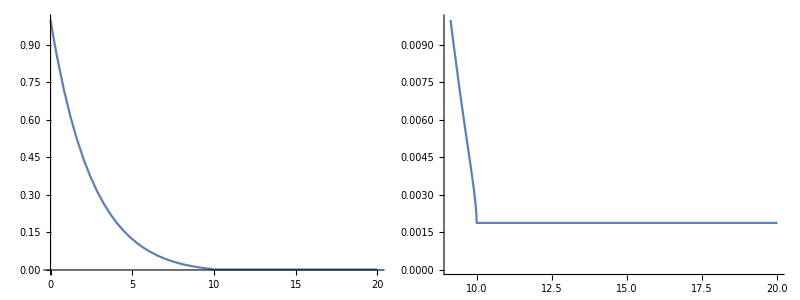

```mathematica
parl={EA->-5,EB->-5,XA->1,XB->XA+l,H->1,m->1};
Grid[{{Plot[Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧//.parl]]^2,{l,0,20},PlotRange->All,ImageSize->400,AxesOrigin->{0,0}],Plot[Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧//.parl]]^2,{l,0,20},PlotRange->{All,{0,0.01}},ImageSize->400]}}]
```

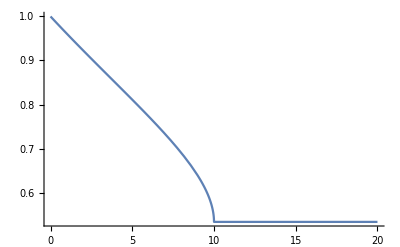

```mathematica
parl={EA->-5,EB->-5,XA->1,XB->XA+l,H->10,m->1};
Grid[{{Plot[Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧//.parl]]^2,{l,0,20},PlotRange->All,ImageSize->400,AxesOrigin->{0,0}]}}]
```

The probability becomes constant at separations equal or larger to the critical separation. Increasing H increases the this constant.

#### Vary probability wrt. H for different separations l={2,10,12,20}

```mathematica
Prob=Abs[Exp[ⅈ Scl[n]/.solN⟦1⟧/.solINI⟦1⟧]]^2;
```

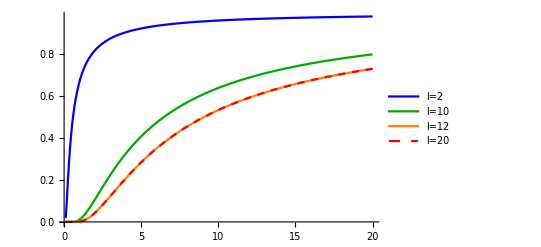
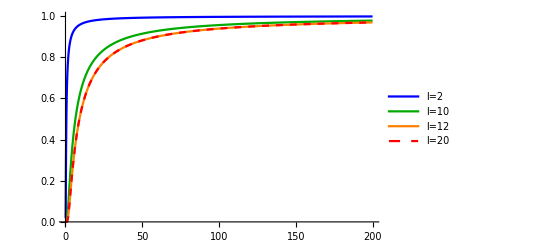
-Graphics- | -Graphics-

```mathematica
parH={EA->-5,EB->-5,XA->1,m->1};
Grid[{{Plot[{Prob//.parH/.XB->2,Prob//.parH/.XB->10,Prob//.parH/.XB->12,Prob//.parH/.XB->20},{H,0.1,20},PlotRange->All,PlotStyle->{Blue,Darker[Green],Orange,{Red,Dashed}},ImageSize->400,PlotLegends->{"l=2","l=10","l=12","l=20"}],Plot[{Prob//.parH/.XB->2,Prob//.parH/.XB->10,Prob//.parH/.XB->12,Prob//.parH/.XB->20},{H,0.1,200},PlotRange->All,PlotStyle->{Blue,Darker[Green],Orange,{Red,Dashed}},ImageSize->400,PlotLegends->{"l=2","l=10","l=12","l=20"}]}}]
```

Above the critical separation of l=XB-XA=10 the probability changes with H in the same way.